```mathematica
Determining Se and Sm from the skyrmion field
```

```mathematica
R  = 1;
θ[r]:= π(1-Exp[-r^2/R^2]); (*Azimuthal angle*)
Integrate[2π r (Cos[θ[r]]+1),{r,0,Infinity}]
SeCoefficient=%//N
Sm = Integrate[2π r^2 Sin[θ[r]],{r,0,Infinity}]
SmCoefficient=%//N
```

π (EulerGamma-CosIntegral[π]+Log[π])

5.17822

∫_0^∞ 2 π r^2 Sin[(1-ⅇ^(-r^2)) π]ⅆr

6.53068

{-0.499994,0.499994}

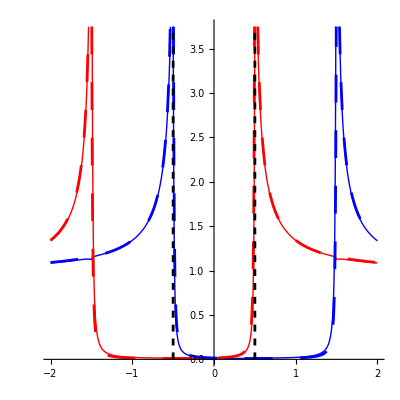

```mathematica
Plotting  LDOS near the skyrmion ;
id =({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}});σx=({{0, 1, 0, 0}, {1, 0, 0, 0}, {0, 0, 0, 1}, {0, 0, 1, 0}}) ; σy=({{0, -ⅈ, 0, 0}, {ⅈ, 0, 0, 0}, {0, 0, 0, -ⅈ}, {0, 0, ⅈ, 0}}); σz =({{1, 0, 0, 0}, {0, -1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, -1}}); τx = ({{0, 0, 1, 0}, {0, 0, 0, 1}, {1, 0, 0, 0}, {0, 1, 0, 0}}); τz =({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, -1, 0}, {0, 0, 0, -1}});
p = 1; m = π 0.01;ρ= m/(2π);  (*Fermi momentum, mass, and DOS*)
Δ = 0.1;S = 0.5Δ;  (*Gap and external magnetization*)
R =2;  Se = R^2 S SeCoefficient; Sm = R^3 S SmCoefficient;(*Parameters of skyrmion: size and effective out-of-plane spin, effective in-plane monopole moment*)

 X =Se π ρ;  ES =  (1-X^2)/(1+X^2);  (*position of conventional YSR state*)
Γ= 0.001; (*imaginary infinitesimal*)
ClearAll["ω","LDOS","G","barG"]

G[ω_]:=-π ρ ((id+σz)/2) .(((ω+ⅈ Γ-S)id +Δ τx)/(√(Δ^2-(ω+ⅈ Γ-S)^2)))-π ρ ((id-σz)/2) .(((ω+ⅈ Γ+S)id +Δ τx)/(√(Δ^2-(ω+ⅈ Γ+S)^2)));
barG[ω_]:= -π ρ ((id-σz)/2) .(((ω+ⅈ Γ-S)id +Δ τx)/(√(Δ^2-(ω+ⅈ Γ-S)^2)))-π ρ ((id+σz)/2) .(((ω+ⅈ Γ+S)id +Δ τx)/(√(Δ^2-(ω+ⅈ Γ+S)^2)));
T[ω_]:=Inverse[id+Se σz.G[ω]-Sm^2 p^2 G[ω].barG[ω]].(-Se σz+Sm^2 p^2 barG[ω]);

LDOSσ[ω_,σ_]:= -1/π Im[Tr[((id+τz)/2).((id+σ)/2).(G[ω]+G[ω].T[ω].G[ω])]];
LDOSσAwayFromSkyrmion[ω_,σ_]:= -1/π Im[Tr[((id+τz)/2).((id+σ)/2).G[ω]]];


Plot LDOS;

gr1 = Plot[{LDOSσ[Δ ω,σz]/ρ,LDOSσ[Δ ω,-σz]/ρ,LDOSσAwayFromSkyrmion[Δ ω,σz]/ρ,LDOSσAwayFromSkyrmion[Δ ω,-σz]/ρ},{ω,-2,2},PlotStyle->{{Thick,Blue},{Thick, Red},{Thick,Blue,Thickness[0.005],Dashing[0.05]},{Thick, Red,Thickness[0.005],Dashing[0.05]},{Thick, Black},{Thickness[0.01],Dashing[0.05],Green//Darker}},
TicksStyle-> Directive[18],AspectRatio->1];


Solution for the  T-matrix poles;


ClearAll["ω","G","barG"]
G=-π ρ ((id+σz)/2) .(((ω-S)id +Δ τx)/(√(Δ^2-(ω-S)^2)))-π ρ ((id-σz)/2) .(((ω+S)id +Δ τx)/(√(Δ^2-(ω+S)^2)));
barG  = -π ρ ((id-σz)/2) .(((ω-S)id +Δ τx)/(√(Δ^2-(ω-S)^2)))-π ρ ((id+σz)/2) .(((ω+S)id +Δ τx)/(√(Δ^2-(ω+S)^2)));
(*Find determinant and find roots*)
ListOfTmatrixPoles=(ω/.NSolve[ Simplify[Det[id+Se σz.G-Sm^2 p^2 G.barG]]==0,ω])/Δ
maxY = PlotRange/.AbsoluteOptions[gr1,PlotRange] //Flatten//Last;
VerticalLine [ω_] := Line[{{ω,0},{ω,maxY }}];
gr2 = Graphics[{Black,Dashed,Thickness[0.005],VerticalLine /@ ListOfTmatrixPoles}];



Show[gr1,gr2]
```